# C. Sun Trial

```mathematica
(* Independent of θf *)
```

## Constants and Parameters (150 MeV 0.5% bw)

```mathematica
(*Constants*)
re=2.8179403262*10^-15;
clight=299792458;
hbar=1.0545718*10^-34;
me=0.511*10^6; (*mc^2 really*)
elecharge=1.60217662*10^-19;
```

```mathematica
(*Parameters*)
Ee=150*10^6;
Q=32*10^-12;
Epulse=62*10^-6;
λ=1064*10^-9;
θcol=0.435*10^-3;
ϕ=0;
ϵnx=0.3*10^-6;
βx=0.126976;
σL=25*10^-6;
ΔEe=5*10^-4; (*relative energy spread*)
L=10; (*ICS source to collimator distance*)
θobs=0;
```

## Observation Angle

```mathematica
θob[θx_,yc_,L_]:=Sqrt[θx^2+(yc/L)^2];
```

## SPE Intermediaries

```mathematica
(*Intermediary calculations for the scattered photon energy*)
γ[Ee_]:=Ee/me;
β[Ee_]:=Sqrt[1-1/γ[Ee]^2];
EL[λ_]:=(2*π*hbar*clight)/(λ*elecharge); (*in eV, using hbar*)
```

## Scattered Photon Energy Calc

```mathematica
Eγ[λ_,Ee_,ϕ_,θobs_]:=(EL[λ]*(1-β[Ee]*Cos[π-ϕ]))/(1-β[Ee]*Cos[θobs]+EL[λ]/Ee*(1-Cos[π-2*θobs]));
```

## CSUN Preliminaries + Collimation

```mathematica
(*Preliminaries*)
Ne[Q_]:=Q/elecharge;
NL[Epulse_,λ_]:=Epulse/(EL[λ]*elecharge);
ϵx[Ee_,ϵnx_]:=ϵnx/γ[Ee];
k[λ_]:=EL[λ]/(hbar*clight);
zr[λ_,σL_]:=(π*σL^2)/λ;
σe[ΔEe_,Ee_]:=ΔEe*Ee; (*Conversion from relative*)
```

```mathematica
(*Collimation*)
R[L_,θcol_]:=L*θcol;
x0[L_,θcol_]:=R[L,θcol]; (*Condition for circular collimator*) 
y0[L_,θcol_]:=R[L,θcol];
```

## CSUN Intermediaries

```mathematica
a[λ_]:=EL[λ]/me;
γbar[λ_,Ee_,ϕ_,θx_,yc_,L_,θobs_]:=(2*Eγ[λ,Ee,ϕ,θobs]*a[λ])/(4*EL[λ]-Eγ[λ,Ee,ϕ,θobs]*θob[θx,yc,L]^2)*(1+Sqrt[1+(4*EL[λ]-Eγ[λ,Ee,ϕ,θobs]*θob[θx,yc,L]^2)/(4*a[λ]^2*Eγ[λ,Ee,ϕ,θobs])]);
ξx[βx_,L_,λ_,Ee_,ϵnx_,σL_]:=1+(βx/L)^2+(2*k[λ]*βx*ϵx[Ee,ϵnx])/zr[λ,σL];
ζx[λ_,βx_,Ee_,ϵnx_,σL_]:=1+(2*k[λ]*βx*ϵx[Ee,ϵnx])/zr[λ,σL];
σθx[Ee_,ϵnx_,βx_,L_,λ_,σL_]:=Sqrt[(ϵx[Ee,ϵnx]*ξx[βx,L,λ,Ee,ϵnx,σL])/(βx*ζx[λ,βx,Ee,ϵnx,σL])];
σγ[ΔEe_,Ee_]:=σe[ΔEe,Ee]/me;
θxmax[λ_,Ee_,ϕ_,yc_,L_,θobs_]:=Sqrt[(4*EL[λ])/Eγ[λ,Ee,ϕ,θobs]-(yc/L)^2];
```

## CSUN Calc

```mathematica
(*Prefactor*)
prefactor[L_,Q_,Epulse_,λ_,σL_,βx_,Ee_,ϵnx_,ΔEe_]:=(re^2*L^2*Ne[Q]*NL[Epulse,λ])/(2*π^2*hbar*clight*zr[λ,σL]*Sqrt[ζx[λ,βx,Ee,ϵnx,σL]]*σγ[ΔEe,Ee]*σθx[Ee,ϵnx,βx,L,λ,σL]);
prefactor[L,Q,Epulse,λ,σL,βx,Ee,ϵnx,ΔEe]
```

1.52552×10^18

```mathematica
(*Separated Integral Terms*)
(*Term 1*)
term1[λ_,Ee_,ϕ_,θx_,yc_,L_,θobs_]:=γbar[λ,Ee,ϕ,θx,yc,L,θobs]/(1+2*γbar[λ,Ee,ϕ,θx,yc,L,θobs]*a[λ]);
NIntegrate[term1[λ,Ee,ϕ,θx,yc,L,θobs],{yc,-y0[L,θcol],y0[L,θcol]},{xc,-x0[L,θcol],x0[L,θcol]},{θx,-θxmax[λ,Ee,ϕ,yc,L,θobs],θxmax[λ,Ee,ϕ,yc,L,θobs]}]
```

0.000237584

```mathematica
(*Term2*)
term2[λ_,Ee_,ϕ_,θx_,yc_,L_,θobs_]:=1/4*((4*γbar[λ,Ee,ϕ,θx,yc,L,θobs]^2*EL[λ])/(Eγ[λ,Ee,ϕ,θobs]*(1+γbar[λ,Ee,ϕ,θx,yc,L,θobs]^2*θob[θx,yc,L]^2))+(Eγ[λ,Ee,ϕ,θobs]*(1+γbar[λ,Ee,ϕ,θx,yc,L,θobs]^2*θob[θx,yc,L]^2))/(4*γbar[λ,Ee,ϕ,θx,yc,L,θobs]^2*EL[λ]));
NIntegrate[term2[λ,Ee,ϕ,θx,yc,L,θobs],{yc,-y0[L,θcol],y0[L,θcol]},{xc,-x0[L,θcol],x0[L,θcol]},{θx,-θxmax[λ,Ee,ϕ,yc,L,θobs],θxmax[λ,Ee,ϕ,yc,L,θobs]}]
```

2.57495×10^-7

```mathematica
(*Term3*)
term3[θx_,xc_,L_,Ee_,ϕ_,ϵnx_,βx_,λ_,σL_,yc_,ΔEe_]:=Exp[(-(θx-xc/L)^2)/(2*σθx[Ee,ϵnx,βx,L,λ,σL]^2)-(γbar[λ,Ee,ϕ,θx,yc,L,θobs]-γ[Ee])^2/(2*σγ[ΔEe,Ee]^2)];
NIntegrate[term3[θx,xc,L,Ee,ϕ,ϵnx,βx,λ,σL,yc,ΔEe],{yc,-y0[L,θcol],y0[L,θcol]},{xc,-x0[L,θcol],x0[L,θcol]},{θx,-θxmax[λ,Ee,ϕ,yc,L,θobs],θxmax[λ,Ee,ϕ,yc,L,θobs]}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

1.03244×10^-9

```mathematica
(*Integral Term*)
intterm[λ_,Ee_,ϕ_,θx_,yc_,L_,θobs_,xc_,ϵnx_,βx_,σL_,ΔEe_]:=term1[λ,Ee,ϕ,θx,yc,L,θobs]*term2[λ,Ee,ϕ,θx,yc,L,θobs]*term3[θx,xc,L,Ee,ϕ,ϵnx,βx,λ,σL,yc,ΔEe];
NIntegrate[intterm[λ,Ee,ϕ,θx,yc,L,θobs,xc,ϵnx,βx,σL,ΔEe],{yc,-y0[L,θcol],y0[L,θcol]},{xc,-x0[L,θcol],x0[L,θcol]},{θx,-θxmax[λ,Ee,ϕ,yc,L,θobs],θxmax[λ,Ee,ϕ,yc,L,θobs]}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

1.51391×10^-7

```mathematica
(*Full Calc + Evaluation*)
```

```mathematica
dNγdEγ[L_,Q_,Epulse_,λ_,σL_,βx_,Ee_,ϵnx_,ΔEe_,ϕ_,θobs_]:=prefactor[L,Q,Epulse,λ,σL,βx,Ee,ϵnx,ΔEe]*NIntegrate[intterm[λ,Ee,ϕ,θx,yc,L,θobs,xc,ϵnx,βx,σL,ΔEe],{yc,-y0[L,θcol],y0[L,θcol]},{xc,-x0[L,θcol],x0[L,θcol]},{θx,-θxmax[λ,Ee,ϕ,yc,L,θobs],θxmax[λ,Ee,ϕ,yc,L,θobs]}]
dNγdEγ[L,Q,Epulse,λ,σL,βx,Ee,ϵnx,ΔEe,ϕ,θobs]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

2.3095×10^11

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

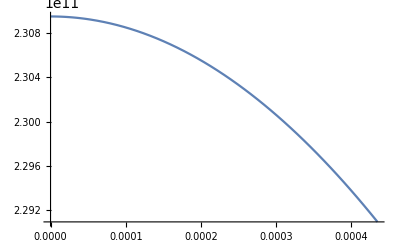

```mathematica
(*Full angular range, 0 to 1/γ*)
Plot[dNγdEγ[L,Q,Epulse,λ,σL,βx,Ee,ϵnx,ΔEe,ϕ,θ],{θ,0,θcol},PlotRange->{{0,θcol},{dNγdEγ[L,Q,Epulse,λ,σL,βx,Ee,ϵnx,ΔEe,ϕ,θcol],dNγdEγ[L,Q,Epulse,λ,σL,βx,Ee,ϵnx,ΔEe,ϕ,0]}}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

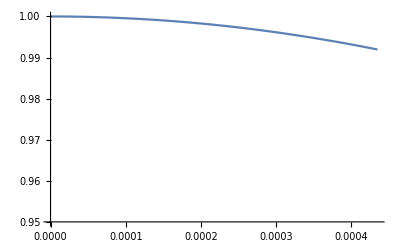

```mathematica
(*Normalised Plot*)
Plot[dNγdEγ[L,Q,Epulse,λ,σL,βx,Ee,ϵnx,ΔEe,ϕ,θ]/dNγdEγ[L,Q,Epulse,λ,σL,βx,Ee,ϵnx,ΔEe,ϕ,0],{θ,0,θcol},PlotRange->{{0,θcol},{0.95,1}}]
```